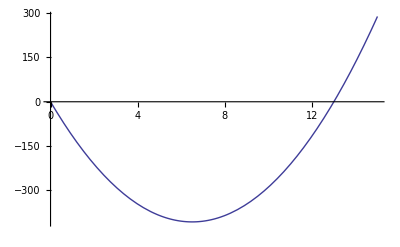

dmax = 0.923077

rL = 48.Ω

L = 403.846uH

{0.00040625,{vout→6.5}}

{4.,{x→0.}}

4.

```mathematica
ClearAll["Global`*"]
vomin = 0;
vomax = 12;
f = 50000;
cLab = 5*10^-6;
esrLab = 1;
iLavg =.25;
ioMax = .4;

vsmax = 15;
vsmin = 13;

T = 1/f;
dmax = vomax/vsmin;
dmin = vomin/vsmax;
ton = T*dmax;
toff = T-ton;
rL = vomax/iLavg;

lir = .4; (*inductor current ratio*)
vo = vomax;
vo = 7;
vs = vsmin;
vs = 13;
L= (vs-vo)*(vo/vs)*T/(lir*ioMax);

Plot[L== 10^6*(vs-v1)*(v1/vs)*T/(lir*ioMax),{v1,0,15}]

Print["dmax = ",N[dmax]];
Print["rL = ",rL,"Ω"];
Print["L = ",L*10^6,"uH"]

Lmin[vout_]:= (vs-vout)*(vout/vs)*T/(lir*ioMax);
FindMaximum[Lmin[vout],{vout,0}]
y[x_]:=-x^2+4;
FindMaximum[y[x],{x,-1}]
FindMaximum[y[x],{x,-1}][[1]]
```